Using the following structure as an example: `[false, true, [[6, 7, 8, 9, 10, 11], 100], 1, 2, 3, 4, 5, false]` (Translation to wolfram language is just replacing [] -> {})
If we ignore additional structure at the vertices, we simply get the following hyperedge: (Any values at the vertices will be definable as additional structure).

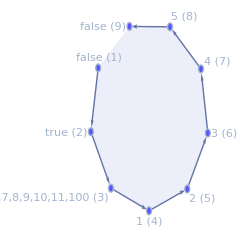

```mathematica
ResourceFunction["WolframModelPlot"][{{"false (1)","true (2)","6,7,8,9,10,11,100 (3)","1 (4)","2 (5)","3 (6)","4 (7)","5 (8)","false (9)"}},VertexLabels->All,VertexStyle-><|"false (1)"->Lighter@Blue,"true (2)"->Lighter@Blue,"6,7,8,9,10,11,100 (3)"->Lighter@Blue,"1 (4)"->Lighter@Blue,"2 (5)"->Lighter@Blue,"3 (6)"->Lighter@Blue,"4 (7)"->Lighter@Blue,"5 (8)"->Lighter@Blue,"false (9)"->Lighter@Blue|>]
```

In this construction, I’m using this merely for visualization, if you see two edges here, that means I have not defined additional structure there, you could say “I can’t even see the edges are there to begin with”. I need additional structure to define the edges, I do that the following way, quite similar to the “Edges as Places” thing:

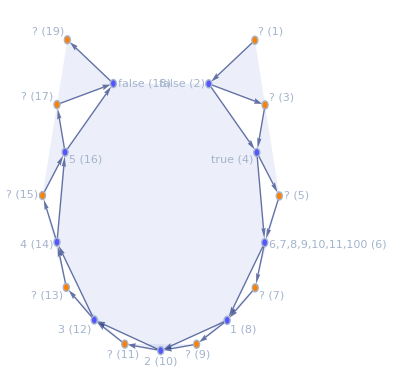

```mathematica
ResourceFunction["WolframModelPlot"][{{"? (1)","false (2)","? (3)"},{"false (2)","true (4)","6,7,8,9,10,11,100 (6)","1 (8)","2 (10)","3 (12)","4 (14)","5 (16)","false (18)"},{"? (3)","true (4)","? (5)"},{"? (5)","6,7,8,9,10,11,100 (6)","? (7)"},{"? (7)","1 (8)","? (9)"},{"? (9)","2 (10)","? (11)"},{"? (11)","3 (12)","? (13)"},{"? (13)","4 (14)","? (15)"},{"? (15)","5 (16)","? (17)"},{"? (17)","false (18)","? (19)"}},VertexLabels->All,VertexStyle-><|"? (1)"->Orange,"false (2)"->Lighter@Blue,"? (3)"->Orange,"true (4)"->Lighter@Blue,"? (5)"->Orange,"6,7,8,9,10,11,100 (6)"->Lighter@Blue,"? (7)"->Orange,"1 (8)"->Lighter@Blue,"? (9)"->Orange,"2 (10)"->Lighter@Blue,"? (11)"->Orange,"3 (12)"->Lighter@Blue,"? (13)"->Orange,"4 (14)"->Lighter@Blue,"? (15)"->Orange,"5 (16)"->Lighter@Blue,"? (17)"->Orange,"false (18)"->Lighter@Blue,"? (19)"->Orange|>]
```

If we interpret the “Vertices” here as merely as describing additional hyperedges, the following construction is what one means with a Vertex: (essentially “lifting the different level of description”)

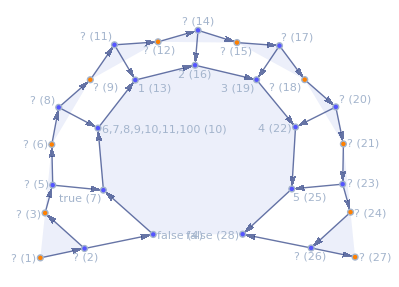

```mathematica
ResourceFunction["WolframModelPlot"][{{"? (1)","? (2)","? (3)"},{"false (4)","true (7)","6,7,8,9,10,11,100 (10)","1 (13)","2 (16)","3 (19)","4 (22)","5 (25)","false (28)"},{"? (2)","false (4)"},{"? (3)","? (5)","? (6)"},{"? (5)","true (7)"},{"? (6)","? (8)","? (9)"},{"? (8)","6,7,8,9,10,11,100 (10)"},{"? (9)","? (11)","? (12)"},{"? (11)","1 (13)"},{"? (12)","? (14)","? (15)"},{"? (14)","2 (16)"},{"? (15)","? (17)","? (18)"},{"? (17)","3 (19)"},{"? (18)","? (20)","? (21)"},{"? (20)","4 (22)"},{"? (21)","? (23)","? (24)"},{"? (23)","5 (25)"},{"? (24)","? (26)","? (27)"},{"? (26)","false (28)"}},VertexLabels->All,VertexStyle-><|"? (1)"->Orange,"? (2)"->Lighter@Blue,"? (3)"->Orange,"false (4)"->Lighter@Blue,"? (5)"->Lighter@Blue,"? (6)"->Orange,"true (7)"->Lighter@Blue,"? (8)"->Lighter@Blue,"? (9)"->Orange,"6,7,8,9,10,11,100 (10)"->Lighter@Blue,"? (11)"->Lighter@Blue,"? (12)"->Orange,"1 (13)"->Lighter@Blue,"? (14)"->Lighter@Blue,"? (15)"->Orange,"2 (16)"->Lighter@Blue,"? (17)"->Lighter@Blue,"? (18)"->Orange,"3 (19)"->Lighter@Blue,"? (20)"->Lighter@Blue,"? (21)"->Orange,"4 (22)"->Lighter@Blue,"? (23)"->Lighter@Blue,"? (24)"->Orange,"5 (25)"->Lighter@Blue,"? (26)"->Lighter@Blue,"? (27)"->Orange,"false (28)"->Lighter@Blue|>]
```

This way we could imagine arbitrarily levels of description as defining what the vertices mean. Essentially: The vertices (or any hyperedge for that matter, if taken as a “reference frame”) define what one ignores, essentially resulting in the construction where the two blue “parts” of a vertex (hyperedge) ; are rendered on top of each other. - Since I heard it mentioned on the 2023/11/24 livestream, I suspect one can then take any hyperedge, and say it’s homotopically equivalent in that direction (if we ignore additional structure defined at each vertex - or we say “don’t ignore it, if it’s a thing like this *pattern* - as that would be deemed an ‘obstruction’”).

Similarly, we can add structure to the vertices (hyperedges) which are references to edges/boundaries (the orange points in the picture above). By adding structure one can imagine adding additional continuations on there, essentially this is what one means with “branches”.

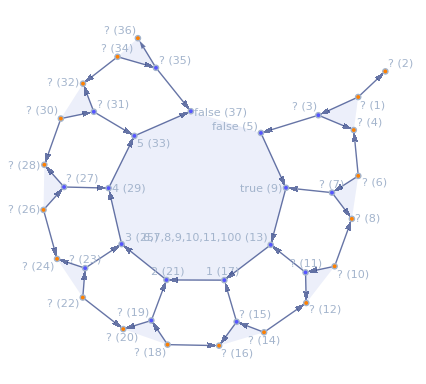

```mathematica
ResourceFunction["WolframModelPlot"][{{"? (1)","? (2)"},{"? (1)","? (3)","? (4)"},{"false (5)","true (9)","6,7,8,9,10,11,100 (13)","1 (17)","2 (21)","3 (25)","4 (29)","5 (33)","false (37)"},{"? (3)","false (5)"},{"? (6)","? (4)"},{"? (6)","? (7)","? (8)"},{"? (7)","true (9)"},{"? (10)","? (8)"},{"? (10)","? (11)","? (12)"},{"? (11)","6,7,8,9,10,11,100 (13)"},{"? (14)","? (12)"},{"? (14)","? (15)","? (16)"},{"? (15)","1 (17)"},{"? (18)","? (16)"},{"? (18)","? (19)","? (20)"},{"? (19)","2 (21)"},{"? (22)","? (20)"},{"? (22)","? (23)","? (24)"},{"? (23)","3 (25)"},{"? (26)","? (24)"},{"? (26)","? (27)","? (28)"},{"? (27)","4 (29)"},{"? (30)","? (28)"},{"? (30)","? (31)","? (32)"},{"? (31)","5 (33)"},{"? (34)","? (32)"},{"? (34)","? (35)","? (36)"},{"? (35)","false (37)"}},VertexLabels->All,VertexStyle-><|"? (1)"->Orange,"? (2)"->Orange,"? (3)"->Lighter@Blue,"? (4)"->Orange,"false (5)"->Lighter@Blue,"? (6)"->Orange,"? (7)"->Lighter@Blue,"? (8)"->Orange,"true (9)"->Lighter@Blue,"? (10)"->Orange,"? (11)"->Lighter@Blue,"? (12)"->Orange,"6,7,8,9,10,11,100 (13)"->Lighter@Blue,"? (14)"->Orange,"? (15)"->Lighter@Blue,"? (16)"->Orange,"1 (17)"->Lighter@Blue,"? (18)"->Orange,"? (19)"->Lighter@Blue,"? (20)"->Orange,"2 (21)"->Lighter@Blue,"? (22)"->Orange,"? (23)"->Lighter@Blue,"? (24)"->Orange,"3 (25)"->Lighter@Blue,"? (26)"->Orange,"? (27)"->Lighter@Blue,"? (28)"->Orange,"4 (29)"->Lighter@Blue,"? (30)"->Orange,"? (31)"->Lighter@Blue,"? (32)"->Orange,"5 (33)"->Lighter@Blue,"? (34)"->Orange,"? (35)"->Lighter@Blue,"? (36)"->Orange,"false (37)"->Lighter@Blue|>]
```

The only thing needed to make branches here is merely to define additional intersections of the vertex; or adding higher arity to the hyperedges (between, or extending the orange points).

Now if we go back to the previous one, for more clarity on the next step:

We can use the same construction, to construct the values we have at the vertices, which, if we disconnect if from the main graph, would look like this (remember that the connected blue points are definitions of vertices, and the linked hyperedges at the orange points are describing their connectivity):

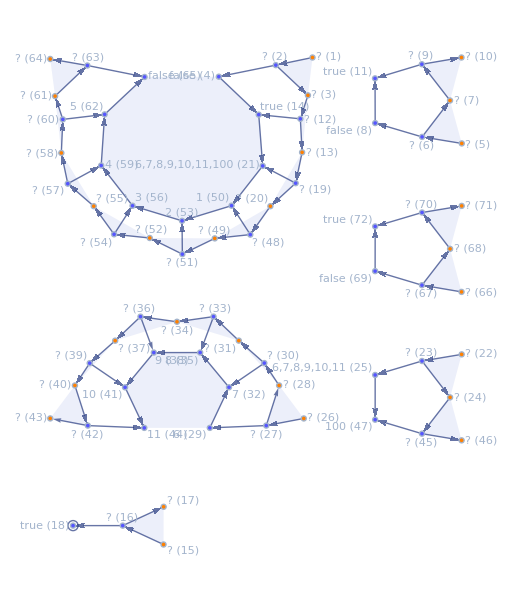

If we glue the larger pieces together (e.g., extending the hyperedge which defines the vertex to the additional structure), it would look something like this:

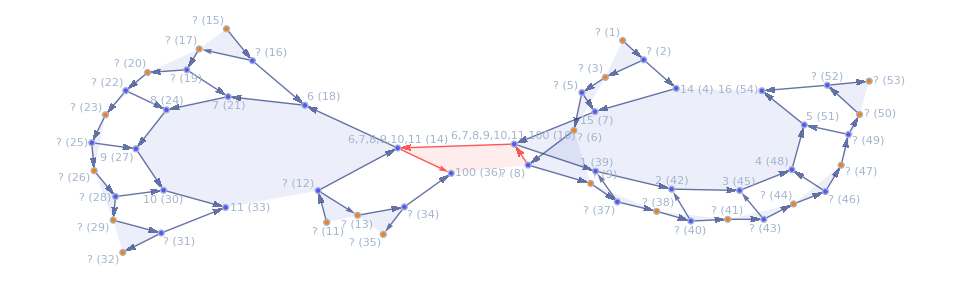

```mathematica
ResourceFunction["WolframModelPlot"][{{"? (1)","? (2)","? (3)"},{"14 (4)","15 (7)","6,7,8,9,10,11,100 (10)","1 (39)","2 (42)","3 (45)","4 (48)","5 (51)","16 (54)"},{"? (2)","14 (4)"},{"? (3)","? (5)","? (6)"},{"? (5)","15 (7)"},{"? (6)","? (8)","? (9)"},{"? (8)","6,7,8,9,10,11,100 (10)","6,7,8,9,10,11 (14)","100 (36)"},{"? (11)","? (12)","? (13)"},{"? (12)","6,7,8,9,10,11 (14)","6 (18)","7 (21)","8 (24)","9 (27)","10 (30)","11 (33)"},{"? (15)","? (16)","? (17)"},{"? (16)","6 (18)"},{"? (17)","? (19)","? (20)"},{"? (19)","7 (21)"},{"? (20)","? (22)","? (23)"},{"? (22)","8 (24)"},{"? (23)","? (25)","? (26)"},{"? (25)","9 (27)"},{"? (26)","? (28)","? (29)"},{"? (28)","10 (30)"},{"? (29)","? (31)","? (32)"},{"? (31)","11 (33)"},{"? (13)","? (34)","? (35)"},{"? (34)","100 (36)"},{"? (9)","? (37)","? (38)"},{"? (37)","1 (39)"},{"? (38)","? (40)","? (41)"},{"? (40)","2 (42)"},{"? (41)","? (43)","? (44)"},{"? (43)","3 (45)"},{"? (44)","? (46)","? (47)"},{"? (46)","4 (48)"},{"? (47)","? (49)","? (50)"},{"? (49)","5 (51)"},{"? (50)","? (52)","? (53)"},{"? (52)","16 (54)"}},VertexLabels->All,VertexStyle-><|"? (1)"->Orange,"? (2)"->Lighter@Blue,"? (3)"->Orange,"14 (4)"->Lighter@Blue,"? (5)"->Lighter@Blue,"? (6)"->Orange,"15 (7)"->Lighter@Blue,"? (8)"->Lighter@Blue,"? (9)"->Orange,"6,7,8,9,10,11,100 (10)"->Lighter@Blue,"? (11)"->Orange,"? (12)"->Lighter@Blue,"? (13)"->Orange,"6,7,8,9,10,11 (14)"->Lighter@Blue,"? (15)"->Orange,"? (16)"->Lighter@Blue,"? (17)"->Orange,"6 (18)"->Lighter@Blue,"? (19)"->Lighter@Blue,"? (20)"->Orange,"7 (21)"->Lighter@Blue,"? (22)"->Lighter@Blue,"? (23)"->Orange,"8 (24)"->Lighter@Blue,"? (25)"->Lighter@Blue,"? (26)"->Orange,"9 (27)"->Lighter@Blue,"? (28)"->Lighter@Blue,"? (29)"->Orange,"10 (30)"->Lighter@Blue,"? (31)"->Lighter@Blue,"? (32)"->Orange,"11 (33)"->Lighter@Blue,"? (34)"->Lighter@Blue,"? (35)"->Orange,"100 (36)"->Lighter@Blue,"? (37)"->Lighter@Blue,"? (38)"->Orange,"1 (39)"->Lighter@Blue,"? (40)"->Lighter@Blue,"? (41)"->Orange,"2 (42)"->Lighter@Blue,"? (43)"->Lighter@Blue,"? (44)"->Orange,"3 (45)"->Lighter@Blue,"? (46)"->Lighter@Blue,"? (47)"->Orange,"4 (48)"->Lighter@Blue,"? (49)"->Lighter@Blue,"? (50)"->Orange,"5 (51)"->Lighter@Blue,"? (52)"->Lighter@Blue,"? (53)"->Orange,"16 (54)"->Lighter@Blue|>, EdgeStyle-><|{"? (8)", "6,7,8,9,10,11,100 (10)", "6,7,8,9,10,11 (14)", "100 (36)"} -> Lighter@Red|>]
```

The rendering being a bit clunky as it’s not really designed for this, but it somewhat works. Notice that the only thing we did here is extent the definition of the vertex (hyperedge) to a higher-arity (more edges) - highlighted in red. - (I think the rendering here isn’t quite right - but it should get the idea across)

Continuity here merely either being the continuation of the hyperedge (basically “I can’t even ask the question of what’s in between”), or in case that one has that ability and can always ask “what’s in between” then continuity is merely a loop:

-Graphics-
In this case the “orange” point could be conceptualized as saying “what’s in between” or “the definition of the edge”. - And continuity is connecting the vertex’s definition (e.g. the hyperedges between the blue points) in a a loop. - Though you may have to construct some way of using it as a rewrite rule here - I’m not that sure about the proper way to construct this yet (if we’re only reasoning from within the hypergraph and don’t go outside it).